## Test on Molecules

## Initialize

### Load images

```mathematica
validationRoot="/Users/Corwin/projects/WolframSummerSchool/uspto-validation-updated";
validationImages="images";
validationResult="molfiles";
validationDumps="dumps";
```

```mathematica
<<"/Users/Corwin/projects/WolframSummerSchool/gitPractice/wss19-ck/Final Project/Drafts/ChemicalLines.wl"
```

```mathematica
SetDirectory["/Users/Corwin/projects/WolframSummerSchool/gitPractice/wss19-ck/Final Project/Outputs"];
```

```mathematica
images=Import[FileNameJoin[{validationRoot,validationDumps,"images.mx"}]];
```

## Set up for outputing graphs

```mathematica
SetDirectory["/Users/Corwin/projects/WolframSummerSchool/presentationOutputs/MoleculeAndGraph"]
```

/Users/Corwin/projects/WolframSummerSchool/presentationOutputs/MoleculeAndGraph

## Run 1

### Image

```mathematica
i=images[[1700]]
```

-Graphics-

### Lines

```mathematica
allLines=doLineDetect[i,0.05,0.01];
showLines[i,allLines]
```

-Graphics-

```mathematica
lineSize=30;
```

```mathematica
longLines=pickLongLines[allLines,lineSize];
showLines[i,longLines]
```

-Graphics-

#### Parallel lines

```mathematica
degreeTolerance=10;
parallelLongLinesByAngle=Gather[Sort[longLines],Not[degreeTolerance<Abs[lineAngle[#1]/Degree-lineAngle[#2]/Degree]<(180-degreeTolerance)]&];
```

```mathematica
Manipulate[HighlightImage[i,Map[{RandomColor[],Tooltip[#,lineAngle[#]/Degree]}&,parallelLongLinesByAngle[[n]]],ImageSize->Small],{n,1,Length[parallelLongLinesByAngle],1}]
```

#### Nearby lines

```mathematica
nearbyParallelLinesByAngle=Map[gatherNearbyLinesByCenter[#,80]&,parallelLongLinesByAngle];
```

```mathematica
Manipulate[HighlightImage[i,nearbyParallelLinesByAngle[[n,m]],ImageSize->Small],{{m,1,"Close Set"},1,10,1},{{n,1,"Parallel Set"},1,Length@nearbyParallelLinesByAngle,1}]
```

#### Intersecting Lines

```mathematica
intersectingNearbyParallelLinesByAngle=Map[gatherIntersectingLines,nearbyParallelLinesByAngle,{2}];
```

#### Merge intersecting lines

```mathematica
singlesA=Cases[intersectingNearbyParallelLinesByAngle,{_Line},{4}];
```

```mathematica
mergeA1=Cases[intersectingNearbyParallelLinesByAngle,{{Repeated[_Line,{2}]}..},{3}];
```

```mathematica
mergeA2Prelim=Cases[intersectingNearbyParallelLinesByAngle,{Repeated[{Repeated[_Line,{2}]},{1,Infinity}],Repeated[{_Line},{1,Infinity}]},{3}];
```

```mathematica
mergeA2=DeleteCases[mergeA2Prelim,{_Line},{2}];
```

```mathematica
mergeA=Join[mergeA1,mergeA2];
```

```mathematica
mergedIntersectingNearbyParallelLinesByAngle= Map[mergeLines,mergeA,{1}];
```

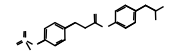

```mathematica
cleanLines=Flatten@Join[singlesA,mergedIntersectingNearbyParallelLinesByAngle];
Graphics[cleanLines,ImageSize->Small]
```

### Vertices

```mathematica
cleanPoints=Sort@Flatten[First/@cleanLines,1];
```

```mathematica
Manipulate[Graphics[{Thin,Gray,cleanLines,Black,Map[Point,Map[Mean,Gather[cleanPoints,EuclideanDistance[#1,#2]<t&]]]},ImageSize->Medium],{t,1,100}]
```

```mathematica
mergedPoints=Map[Point,Map[Mean,Gather[cleanPoints,EuclideanDistance[#1,#2]<30&]]];
```

```mathematica
mergeThreshold=29;
```

```mathematica
cleanPointsGathered=Gather[cleanPoints,EuclideanDistance[#1,#2]<mergeThreshold&];
```

```mathematica
mergedPoints=Point/@Mean/@cleanPointsGathered;
```

```mathematica
mergedPointParents=AssociationThread[mergedPoints,Map[Point,cleanPointsGathered,{2}]];
```

```mathematica
separatePointsChild=Merge[Flatten@Map[Reverse,Thread/@Normal[mergedPointParents],{2}],Identity];
```

#### Tracing Vertices

```mathematica
edgeListTargets=Map[traceConnections[#,cleanLines,mergedPoints,mergedPointParents,separatePointsChild]&,mergedPoints]
```

{{2,2},{1,1,3,3,3,4,5},{2,2,2},{2},{2,6,6,6,6},{9,7,5,6,6,5,6,6,7},{8,6,6},{11,11,7},{10,10,9,9,10,10,9,9,6,10},{9,11,9,9,10,10,9,9,10,10},{8,12,12,10,12,12,8},{13,11,12,12,11,12,12},{15,12},{15,15},{16,14,13,14},{15},{18},{21,17,19,21},{20,18,20},{23,23,23,23,19,19},{22,22,22,22,18,18},{23,23,21,22,22,21,22,22},{22,24,24,23,23,24,24,23,23,22,20,23,23,20,23,23},{25,25,25,25,23,23,24,24,23,23,24,24},{26,27,24,25,25,24,25,25},{25},{25}}

```mathematica
edgePairs=Thread/@Transpose[{Range[Length[edgeListTargets]],edgeListTargets}]
```

{{{1,2},{1,2}},{{2,1},{2,1},{2,3},{2,3},{2,3},{2,4},{2,5}},{{3,2},{3,2},{3,2}},{{4,2}},{{5,2},{5,6},{5,6},{5,6},{5,6}},{{6,9},{6,7},{6,5},{6,6},{6,6},{6,5},{6,6},{6,6},{6,7}},{{7,8},{7,6},{7,6}},{{8,11},{8,11},{8,7}},{{9,10},{9,10},{9,9},{9,9},{9,10},{9,10},{9,9},{9,9},{9,6},{9,10}},{{10,9},{10,11},{10,9},{10,9},{10,10},{10,10},{10,9},{10,9},{10,10},{10,10}},{{11,8},{11,12},{11,12},{11,10},{11,12},{11,12},{11,8}},{{12,13},{12,11},{12,12},{12,12},{12,11},{12,12},{12,12}},{{13,15},{13,12}},{{14,15},{14,15}},{{15,16},{15,14},{15,13},{15,14}},{{16,15}},{{17,18}},{{18,21},{18,17},{18,19},{18,21}},{{19,20},{19,18},{19,20}},{{20,23},{20,23},{20,23},{20,23},{20,19},{20,19}},{{21,22},{21,22},{21,22},{21,22},{21,18},{21,18}},{{22,23},{22,23},{22,21},{22,22},{22,22},{22,21},{22,22},{22,22}},{{23,22},{23,24},{23,24},{23,23},{23,23},{23,24},{23,24},{23,23},{23,23},{23,22},{23,20},{23,23},{23,23},{23,20},{23,23},{23,23}},{{24,25},{24,25},{24,25},{24,25},{24,23},{24,23},{24,24},{24,24},{24,23},{24,23},{24,24},{24,24}},{{25,26},{25,27},{25,24},{25,25},{25,25},{25,24},{25,25},{25,25}},{{26,25}},{{27,25}}}

```mathematica
edgeList=Flatten@Map[UndirectedEdge@@#&,edgePairs,{2}]
```

{1<->2,1<->2,2<->1,2<->1,2<->3,2<->3,2<->3,2<->4,2<->5,3<->2,3<->2,3<->2,4<->2,5<->2,5<->6,5<->6,5<->6,5<->6,6<->9,6<->7,6<->5,6<->6,6<->6,6<->5,6<->6,6<->6,6<->7,7<->8,7<->6,7<->6,8<->11,8<->11,8<->7,9<->10,9<->10,9<->9,9<->9,9<->10,9<->10,9<->9,9<->9,9<->6,9<->10,10<->9,10<->11,10<->9,10<->9,10<->10,10<->10,10<->9,10<->9,10<->10,10<->10,11<->8,11<->12,11<->12,11<->10,11<->12,11<->12,11<->8,12<->13,12<->11,12<->12,12<->12,12<->11,12<->12,12<->12,13<->15,13<->12,14<->15,14<->15,15<->16,15<->14,15<->13,15<->14,16<->15,17<->18,18<->21,18<->17,18<->19,18<->21,19<->20,19<->18,19<->20,20<->23,20<->23,20<->23,20<->23,20<->19,20<->19,21<->22,21<->22,21<->22,21<->22,21<->18,21<->18,22<->23,22<->23,22<->21,22<->22,22<->22,22<->21,22<->22,22<->22,23<->22,23<->24,23<->24,23<->23,23<->23,23<->24,23<->24,23<->23,23<->23,23<->22,23<->20,23<->23,23<->23,23<->20,23<->23,23<->23,24<->25,24<->25,24<->25,24<->25,24<->23,24<->23,24<->24,24<->24,24<->23,24<->23,24<->24,24<->24,25<->26,25<->27,25<->24,25<->25,25<->25,25<->24,25<->25,25<->25,26<->25,27<->25}

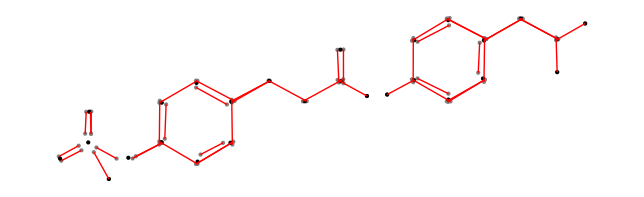

```mathematica
Graphics[{Gray,Point/@cleanPoints,Thick,Black,mergedPoints,Thin,Red,cleanLines}]
```

```mathematica
directedEdgeList=Flatten@Map[DirectedEdge@@#&,edgePairs,{2}];
```

```mathematica
graphOfMolecule=Graph[Range[Length[mergedPoints]],directedEdgeList];
```

```mathematica
{i,Show[graphOfMolecule,AspectRatio->1/GoldenRatio]}
```

{-Graphics-,-Graphics-}

```mathematica
graphPic=Rasterize[graphOfMolecule,ImageResolution->200]
```

-Graphics-

```mathematica
Export["graph1.png",graphPic]
```

graph1.png

```mathematica
noDuplicateEdgePairs=DeleteDuplicates[Sort/@Flatten[edgePairs,1]];
```

```mathematica
noSelfBond=DeleteCases[noDuplicateEdgePairs,{ee_,ee_}];
```

```mathematica
undirectedEdgeList=Map[UndirectedEdge@@#&,noSelfBond,{1}];
```

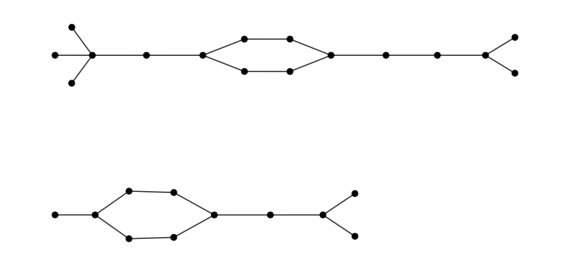

```mathematica
Graph[Range[Length[mergedPoints]],undirectedEdgeList,EdgeStyle->Black,VertexStyle->Black]
```

### Recognize Text

### Molecule

```mathematica
atomList=Table["C",Length[mergedPoints]]
```

{C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C,C}

```mathematica
noDuplicateEdgePairs=DeleteDuplicates[Sort/@Flatten[edgePairs,1]];
```

```mathematica
noSelfBond=DeleteCases[noDuplicateEdgePairs,{ee_,ee_}];
```

```mathematica
bondList=Apply[Bond@*List,noSelfBond,2];
```

```mathematica
molecule=Molecule[atomList,bondList]
```

Molecule[…]